```mathematica
image1:=-Graphics-;
Image2:=ImageCrop[Binarize[image1,0.7],{700,500}];
Image1c:=ImageCrop[image1,{700,500}];
Row[image1,

Manipulate[Colorize[WatershedComponents[FillingTransform[ColorNegate[Image1c],a,Padding->1]],ColorFunction->"Aquamarine"]//Binarize,{a,0,0.3,0.01}]]
(*Binarize[RangeFilter[Image1c,1],0.2](*Ok7*)*)
(*ClusteringComponents[Image1c,3] // Colorize
Image3:=Thinning[Binarize@Image2, Method->"MedialAxis"];Image3*)
```

Row[-Graphics-,]

```mathematica
DistanceTransform[-Graphics-]// ImageAdjust
```

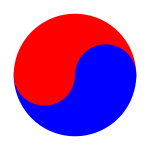
```mathematica
Binarize[-Graphics-,0.2]
```

-Graphics-

{1→{14702.3,{64.8613,87.5951}}}

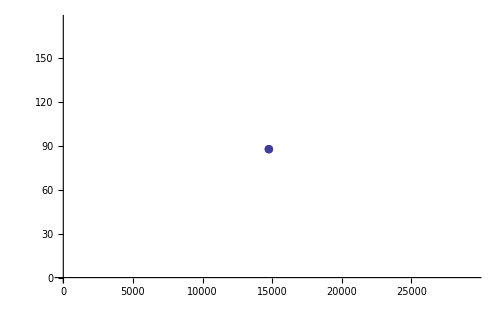

```mathematica
measurements=ComponentMeasurements[-Graphics-,{"Area","Centroid"}]
widthdata={First[#1],Last[#1[[2]]]}&/@measurements[[All,2]];

ListPlot[widthdata,PlotMarkers->{Automatic,Medium}]
```